#### Integration Scratch book

```mathematica
aPrime[t_]:=1+ Pi * Cos[Pi*t]
P[t_]:=11*(1-Exp[-t])+Pi/(1+Pi^2)*(Cos[Pi*t]+Pi*Sin[Pi*t]-Exp[-t])
```

```mathematica
integral=Integrate[aPrime[t]*P[t],{t,0,1}]
N[integral]
```

(22-20 (1+ⅇ) π-(-42+ⅇ) π^2-20 (1+ⅇ) π^3+(22+ⅇ) π^4)/(2 ⅇ (1+π^2)^2)

0.432887

integral

WolframAlphaQueryResults

#### Testing 2.15

```mathematica
K = 11 + Pi / (1 + Pi^2)
```

11+π/(1+π^2)

```mathematica
N[K]
```

11.289

```mathematica
IFull=Integrate[aPrime[t]*(-Exp[-t]*K+Pi/(1+Pi^2)*(Cos[Pi*t]+Pi*Sin[Pi*t])+ 11),{t,0,1}]

N[IFull]
```

(22-20 (1+ⅇ) π-(-42+ⅇ) π^2-20 (1+ⅇ) π^3+(22+ⅇ) π^4)/(2 ⅇ (1+π^2)^2)

0.432887

```mathematica
I1 = Integrate[(-Exp[-t]*K),{t,0,1}]
N[I1]
```

-((-1+ⅇ) (11+π+11 π^2))/(ⅇ (1+π^2))

-7.13603

```mathematica
I2=Integrate[Pi/(1+Pi^2)*(Cos[Pi*t]+Pi*Sin[Pi*t]),{t,0,1}]
N[I2]
```

(2 π)/(1+π^2)

0.578051

```mathematica
I3 = Integrate[11, {t,0,1}]
```

11

```mathematica
I4 = Integrate[Pi Cos[Pi t]* (-Exp[-t]*K),{t,0,1}]
N[I4]
```

-((1+ⅇ) π (11+π+11 π^2))/(ⅇ (1+π^2)^2)

-4.46314

```mathematica
X1 = Integrate[Exp[-t]*Cos[Pi t], {t, 0, 1}]
```

(1+ⅇ)/(ⅇ+ⅇ π^2)

```mathematica
Integrate[Exp[-t]*Cos[Pi t], t]
```

(ⅇ^-t (-Cos[π t]+π Sin[π t]))/(1+π^2)

```mathematica
Integrate[Pi Exp[-t] Cos[Pi t], {t, 0, 1}]
```

((1+ⅇ) π)/(ⅇ+ⅇ π^2)

```mathematica
I5  = Integrate[Pi Cos[Pi t] * Pi/(1+Pi^2)*Cos[Pi*t], {t,0,1}]
N[I5]
```

π^2/(2+2 π^2)

0.454

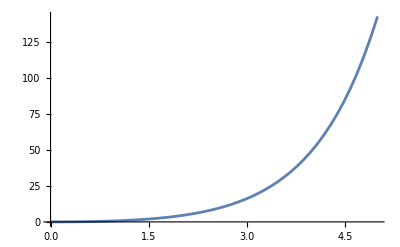

```mathematica
Plot[Exp[y] - 1 -y, {y, 0, 5}]
```